```mathematica
(*
Setup data and reference roots
*)
nbPath=NotebookDirectory[];
nbDepth=FileNameDepth[nbPath];
quiccroot=FileNameJoin[FileNameSplit[nbPath][[1;;nbDepth-4]]];
dataroot=FileNameJoin[Flatten[{quiccroot,"build","Components","Transform","TestSuite"}]];
dataroot::wrongpath="Path to data root does not exist: `1`";
If[!DirectoryQ[dataroot],
Message[dataroot::wrongpath,dataroot];
Abort[];
];

Hyperlink["Energy Tests",{SelectedNotebook[],"energyTests"}]
Hyperlink["Projector Tests",{SelectedNotebook[],"projectorTests"}]
Hyperlink["Integrator Tests",{SelectedNotebook[],"integratorTests"}]
Hyperlink["Backward-Forward loop Tests",{SelectedNotebook[],"bfloopTests"}]
Hyperlink["Power Tests",{SelectedNotebook[],"powerTests"}]
Hyperlink["Radial Power Tests",{SelectedNotebook[],"radialPowerTests"}]
```

Energy Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68energyTestsButtonData

Projector Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68projectorTestsButtonData

Integrator Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68integratorTestsButtonData

Backward-Forward loop Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68bfloopTestsButtonData

Power Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68powerTestsButtonData

Radial Power Testsb4a0dd8d-8a96-431c-a322-50aa4054eb68radialPowerTestsButtonData

```mathematica
(* 
General Worland setup
*)
(*Worland package setup*)
pkgroot=FileNameJoin[Flatten[{quiccroot,"Components","TestSuite","Mathematica"}]];
AppendTo[$Path, pkgroot];
Worland`$mpprec=100;
Worland`$WorlandType="SphEnergy";
Needs["Worland`"];
ParallelNeeds["Worland`"]
$MaxExtraPrecision=1000;
mpprec = Worland`$mpprec;

datadir={"_data","Transform","FiniteDiff","Sphere"};
refdir={"_refdata","Transform","FiniteDiff","Sphere"};

(*intgdivrdrWorland*)
divr[f_,l_,t_]:=Module[{out},
out = Simplify[1/t f];
out]
divrdr[f_,l_,t_]:=Module[{out},
out = Simplify[1/t D[t f,t]];
out]
(* 
Operators to work on grid
*)
WnlEnergy[n_,l_,r_]:=r^l JacobiP[n,$wsphα,l+$wsphdβ,2 r^2-1]/norm[n,$wsphα,l+$wsphdβ]
divrWnlzeroWnl[n_,l_,r_]:= If[l==0,0r,divrWnl[n,l,r]];
dWnlWnl[n_,l_,r_]:= If[l==0,Wnl[n,l,r],dWnl[n,l,r]];
divrdrWnlzeroWnl[n_,l_,r_]:= If[l==0,0r,divrdrWnl[n,l,r]];

uniformRadialGrid[n_]:=N[Table[i/(n-1),{i,0,n-1}],mpprec]

uniformTruncation[maxN_,l_]:=maxN;
dealiasGrid[n_,l_,tFunc_:uniformTruncation]:=Floor[3(tFunc[n,l]+l/2+8)/2];
uniformSetup[maxL_]:=Module[{nN,nR,f},
f=uniformTruncation;
nN=Floor[maxL/2]+1;
nR=dealiasGrid[nN-1,maxL,f];
{nN,nR,f}
];

(*
Tools for generating spectral space spectra 
*)
unitSpectrum[n_,maxN_,l_,tFunc_:uniformTruncation]:=If[n<=tFunc[maxN,l],1,0];
maxSpectrum[n_,maxN_,l_,tFunc_:uniformTruncation]:=If[n==tFunc[maxN,l],1,0];
minSpectrum[n_,maxN_,l_,tFunc_:uniformTruncation]:=If[n==0,1,0];
randSpectrum[n_,maxN_,l_,tFunc_:uniformTruncation]:=Module[{val},
If[n<=tFunc[maxN,l],
val =N[ IntegerPart[RandomReal[{1/10,1}] 10^3]/10^3,mpprec];,
val=0];
val
]
(*
Configure which output to generate
*)
genInDataDefault=False;
genRefDataDefault=False;
generateInData=genInDataDefault;
generateRefData=genRefDataDefault;
configureGenerator[genIn_:genInDataDefault,genRef_:genRefDataDefault]:=
Module[{},
generateInData=genIn;
generateRefData=genRef;
];
(*
Generate metadata
*)
createMetadata[nN_, gridN_,ls_, tFunc_]:=Module[{descr,lModes,mModes,nL=Length@ls,header },
lModes=Flatten[Table[{ls[[i]],1},{i,1,nL}]];
mModes=Flatten[Table[{0,tFunc[nN-1,ls[[i]]]+1},{i,1,nL}]];;
header={
"# Format description",
"# line 1: number of lines",
"# line 2: simulation modal size", 
"# line 3: simulation physical size", 
"# line 4: number of modes nK", 
"# line 5 + 2*k: mode",
"# line 6 + 2*k: number of 2D modes",
"# line (5 + 2*nK) + 2*j: 2D mode",
"# line (6 + 2*nK) + 2*j: number of 1D modes"
};
descr = Flatten[{nN,gridN,nL,lModes,mModes}];
descr = Prepend[descr,Length@descr];
descr = Flatten[Prepend[descr,header]];
descr
];
```

Worland:: Using SphEnergy Worland type

Worland:: Number of digits is set to 100

Energy tests

```mathematica
testEnergy[meta_,id_,infunc_,gfunc_,opfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,tmp,nN,gridN,ls,descr, specR,grid,zg ,in,inI,inR,gq,xLeg,wLeg,rLeg,ref,msg,tempmsg,fbase,fname,tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" FD sphere operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate meta data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[gridN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
specR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
grid = gfunc[gridN];
zg = 0grid;
inR=Table[Sum[If[specR[[i,j]]!=0,tmp=Wnl[i-1,ls[[j]],ζ];tmp=tmp/.{ζ->grid};If[Length@tmp < Length@grid,tmp=Table[tmp,Length@grid]];specR[[i,j]]tmp,zg],{i,1,nN}],{j,1,Length@ls}];
inI = -inR;
in = Join[Transpose[inR],Transpose[inI]];
in=N[in,outprec];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate output referece *)
If[generateInData&&generateRefData,
gq=GaussianQuadratureWeights[4nN+2ls[[-1]]+4,-1,1,mpprec];
xLeg=gq[[;;,1]];wLeg=gq[[;;,2]];rLeg=(xLeg+1)/2;
ref=Table[specR=infunc[i-1,nN-1,ls[[j]],tFunc];tmp=Sum[(specR-specR ⅈ)opfunc[i-1,ls[[j]],rLeg],{i,1,nN}];Chop[1/2 Dot[wLeg,(rLeg^2 Abs[tmp]^2)]],{j,1,Length@ls}];
ref=N[ref,outprec];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testEnergy]={truncationFunc->uniformTruncation};
```

```mathematica
generateEnergies[meta_,tId_,inOp_,gfunc_,OptionsPattern[]]:=Module[{tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
testEnergy[meta,tId,inOp,gfunc,Wnl,"Reductor/EnergyR2",truncationFunc->tFunc];
testEnergy[meta,tId,inOp,gfunc,divrWnlzeroWnl,"Reductor/Energy",truncationFunc->tFunc];
testEnergy[meta,tId,inOp,gfunc,divrdrWnlzeroWnl,"Reductor/EnergyD1R1",truncationFunc->tFunc];
testEnergy[meta,tId,inOp,gfunc,slaplWnl,"Reductor/EnergySLaplR2",truncationFunc->tFunc];
];
Options[generateEnergies]={truncationFunc->uniformTruncation,genIn->False, genRef->False};
```

```mathematica
maxL=18;
genTags={True,True};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
id=(it-1);
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum, id = "<>ToString[id]];
{nN,nR,tFunc}=uniformSetup[maxL];
meta = {nN,nR, {1,2,3,8,maxL}};
generateEnergies[meta,id,spectra[[it]],uniformRadialGrid,truncationFunc->tFunc, genIn->genTags[[1]], genRef->genTags[[2]]];
];
Clear[it,spectra,is,maxL,nN,nR,tFunc,meta,id]
```

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with minSpectrum spectrum, id = 0

Exporting Reductor/EnergyR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:25)

Exporting Reductor/Energy FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:25)

Exporting Reductor/EnergyD1R1 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:25)

Exporting Reductor/EnergySLaplR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:25)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with maxSpectrum spectrum, id = 1

Exporting Reductor/EnergyR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:26)

Exporting Reductor/Energy FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:26)

Exporting Reductor/EnergyD1R1 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:26)

Exporting Reductor/EnergySLaplR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:26)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with unitSpectrum spectrum, id = 2

Exporting Reductor/EnergyR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:27)

Exporting Reductor/Energy FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:27)

Exporting Reductor/EnergyD1R1 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:27)

Exporting Reductor/EnergySLaplR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:28)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with randSpectrum spectrum, id = 3

Exporting Reductor/EnergyR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:28)

Exporting Reductor/Energy FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:28)

Exporting Reductor/EnergyD1R1 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:29)

Exporting Reductor/EnergySLaplR2 FD sphere operator for N = 10, Ng = 39, l = {1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 11:00:29)

```mathematica
genTags={True,True};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
For[ p = 4,p<9,p++,
id=100it+p;
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum, id = "<>ToString[id]];
maxL=2^p-1;
{nN,nR,tFunc}=uniformSetup[maxL];
meta={nN,nR,Table[l,{l,0,maxL}]};
generateEnergies[meta,id,spectra[[it]],,uniformRadialGrid,truncationFunc->tFunc,genIn->genTags[[1]],genRef->genTags[[2]]];
Clear[nL,nN,nR,tFunc,meta];
];
];
Clear[it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

Projector tests

```mathematica
testProjector[meta_,id_,infunc_,gfunc_,opfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,nN,gridN,ls,descr, specR,in,inR,inI,grid,zg,ref,refR,refI,msg,tempmsg,fbase,fname,tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" FD sphere operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate meta data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[gridN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
specR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
grid = gfunc[gridN];
zg = 0grid;
inR=Table[Sum[If[specR[[i,j]]!=0,tmp=Wnl[i-1,ls[[j]],ζ];tmp=tmp/.{ζ->grid};If[Length@tmp < Length@grid,tmp=Table[tmp,Length@grid]];specR[[i,j]]tmp,zg],{i,1,nN}],{j,1,Length@ls}];
inI = -inR;
in = Join[Transpose[inR],Transpose[inI]];
in=N[in,outprec];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData&&generateRefData,
specR=SetPrecision[specR,mpprec];
refR=Table[Sum[If[specR[[i,j]]!=0,tmp=opfunc[i-1,ls[[j]],ζ];tmp=tmp/.{ζ->grid};If[Length@tmp < Length@grid,tmp=Table[tmp,Length@grid]];specR[[i,j]],zg]tmp,{i,1,nN}],{j,1,Length@ls}];
refI=-refR;
ref=Join[Transpose[refR],Transpose[refI]];
ref=N[ref,outprec];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testProjector]={truncationFunc->uniformTruncation};
```

```mathematica
generateProjectors[meta_,tId_,inOp_,gfunc_,OptionsPattern[]]:=Module[{subdir,tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
subdir="Projector/";
testProjector[meta,tId,inOp,gfunc,Wnl,subdir<>"P",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,divrWnl,subdir<>"DivR1",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,dWnl,subdir<>"D1",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,divrdrWnl,subdir<>"DivR1D1R1",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,slaplWnl,subdir<>"SphLapl",truncationFunc->tFunc];

testProjector[meta,tId,inOp,gfunc,divrWnlzeroWnl,subdir<>"DivR1_Zero",truncationFunc->tFunc];
testProjector[meta,tId,inOp,gfunc,divrdrWnlzeroWnl,subdir<>"DivR1D1R1_Zero",truncationFunc->tFunc];
];
Options[generateProjectors]={truncationFunc->uniformTruncation,genIn->False, genRef->False};
```

```mathematica
maxL=18;
genTags={True,True};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
id=(it-1);
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum, id = "<>ToString[id]];
{nN,nR,tFunc}=uniformSetup[maxL];
meta = {nN,nR, {0,1,2,3,8,maxL}};
generateProjectors[meta,id,spectra[[it]],uniformRadialGrid,truncationFunc->uniformTruncation, genIn->genTags[[1]], genRef->genTags[[2]]];
];
Clear[it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with minSpectrum spectrum, id = 0

Exporting Projector/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:11)

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Exporting Projector/DivR1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:11)

Exporting Projector/D1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:11)

Power::infy: Infinite expression 1/0 encountered.

Exporting Projector/DivR1D1R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:12)

Exporting Projector/SphLapl FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:12)

Exporting Projector/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:12)

Exporting Projector/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:12)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with maxSpectrum spectrum, id = 1

Exporting Projector/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:12)

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Exporting Projector/DivR1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:13)

Exporting Projector/D1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:13)

Exporting Projector/DivR1D1R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:13)

Exporting Projector/SphLapl FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:13)

Exporting Projector/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:13)

Exporting Projector/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:13)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with unitSpectrum spectrum, id = 2

Exporting Projector/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:14)

Exporting Projector/DivR1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:14)

Exporting Projector/D1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:14)

Exporting Projector/DivR1D1R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:14)

Exporting Projector/SphLapl FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:14)

Exporting Projector/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:14)

Exporting Projector/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:15)

%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%%

%%% Generating data with randSpectrum spectrum, id = 3

Exporting Projector/P FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:15)

Exporting Projector/DivR1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:15)

Exporting Projector/D1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:15)

Exporting Projector/DivR1D1R1 FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:15)

Exporting Projector/SphLapl FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:16)

Exporting Projector/DivR1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:16)

Exporting Projector/DivR1D1R1_Zero FD sphere operator for N = 10, Ng = 39, l = {0, 1, 2, 3, 8, 18}... Done(Mon 1 Sep 2025 10:59:16)

```mathematica
generateDbProjectors[meta_,tId_,inOp_,gfunc_,OptionsPattern[]]:=Module[{subdir,tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
subdir="Projector/";
testProjector[meta,tId,inOp,gfunc,Wnl,subdir<>"P",truncationFunc->tFunc];
];
Options[generateDbProjectors]={truncationFunc->uniformTruncation,genIn->False,genRef->False};
```

```mathematica
genTags={True,True};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
For[ p = 4,p<7,p++,
id=100it+p;
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum], id = "<>ToString[id]];
maxL=2^p-1;
{nN,nR,tFunc}=uniformSetup[maxL];
meta={nN,nR,Table[l,{l,0,maxL}]};
generateDbProjectors[meta,id,spectra[[it]],wgrid,truncationFunc->tFunc,genIn->genTags[[1]],genRef->genTags[[2]]];
Clear[nL,nN,nR,tFunc,meta];
];
];
Clear[it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

Integrator tests

```mathematica
testIntegrator[meta_,id_,infunc_,outfunc_,gfunc_,wfunc_,inopfunc_,opfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,intN=OptionValue[intN],tFunc=OptionValue[truncationFunc],i,nN,sRows,sCols,gridN,ls,descr, in,inR,inI,s,grid,zg,zs,wgts,ref,refR,refI,msg,tempmsg,fbase,fname},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
msg="Exporting "<>name<>" Worland operator id = "<>ToString[id]<>" for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
fbase=name<>"_id"<>ToString[id];
(* Generate meta data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[nN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
grid = gfunc[gridN];
sRows=If[intN <= 0,nN,intN];
sCols = Length@ls;
s=Table[infunc[i-1,sRows-1,ls[[j]],tFunc],{i,1,sRows},{j,1,sCols}];
zg =0 grid;
inR=Table[Sum[If[s[[i,j]]!=0,s[[i,j]]inopfunc[i-1,ls[[j]],grid],zg],{i,1,sRows}],{j,1,sCols}];
inI = -inR;
in=Join[Transpose[inR],Transpose[inI]];
in=N[in,outprec];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData&& generateRefData,
wgts=wfunc[gridN];
zs=0;
refR=Table[If[i-1<=tFunc[sRows-1,ls[[j]]],Dot[wgts opfunc[i-1,ls[[j]],grid],Transpose[inR[[j,;;]]]],zs],{i,1,sRows},{j,1,sCols}];
refR = Transpose[Table[outfunc[refR[[;;,j]], ls[[j]],tFunc],{j,1,sCols}]];
refI = -refR;
ref = Join[refR[[1;;nN,;;]],refI[[1;;nN,;;]]];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testIntegrator]={intN->-1,truncationFunc->uniformTruncation};
testIntegratorDiff[meta_,id_,infunc_,sfunc_,outfunc_,gfunc_,wfunc_,inopfunc_,opfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,intN=OptionValue[intN],tFunc=OptionValue[truncationFunc],nN,sRows,sCols,gridN,ls,descr,s, in,inR,finR,inI,finI,grid,wgts,ref,refR,refI,msg,tempmsg,fbase,fname},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
msg="Exporting "<>name<>" Worland operator id = " <> ToString[id]<>" for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
fbase=name<>"_id"<>ToString[id];
(* Generate meta data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[nN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
grid = gfunc[gridN];
sRows =If[intN <= 0,nN,intN];
sCols =Length@ls;
s=Table[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,sRows},{j,1,sCols}];
inR=Table[Sum[s[[i,j]]inopfunc[i-1,ls[[j]],grid],{i,1,sRows}],{j,1,sCols}];
inI=-inR;
in=Join[Transpose[inR],Transpose[inI]];
in=N[in,outprec];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData && generateRefData,
wgts=wfunc[gridN];
finR[r_]=Table[Simplify[outfunc[Sum[s[[i,j]]inopfunc[i-1,ls[[j]],r],{i,1,sRows}],ls[[j]],r]],{j,1,sCols}];
finI[r_]:=Table[Simplify[outfunc[Sum[-s[[i,j]]inopfunc[i-1,ls[[j]],r],{i,1,sRows}],ls[[j]],r]],{j,1,sCols}];
inR =Map[finR,grid];
(*inI =Map[finI,grid];*)
inI=-inR;
refR=Table[Dot[wgts opfunc[i-1,ls[[j]],grid],inR[[;;,j]]],{i,1,sRows},{j,1,sCols}];
refR = Transpose[Table[sfunc[refR[[;;,j]], ls[[j]]],{j,1,sCols}]];
refI=-refR;
ref = Join[refR[[1;;nN,;;]],refI[[1;;nN,;;]]];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testIntegratorDiff]={intN->-1,truncationFunc->uniformTruncation};
testIntegratorNL[meta_,id_,infunc_,outfunc_,gfunc_,wfunc_,inopfunc_,opfunc_,name_,OptionsPattern[]]:=
Module[{sRows,nlinfunc},
sRows = 2meta[[1]];
nlinfunc[n_,maxN_,l_,tFunc_:uniformTruncation]:=infunc[n,maxN,l,tFunc]/If[n<= maxN,1,10];
testIntegrator[meta,id,nlinfunc,outfunc,gfunc,wfunc,inopfunc,opfunc,name,intN->OptionValue[intN],truncationFunc->OptionValue[truncationFunc]];
];
Options[testIntegratorNL]={intN->-1,truncationFunc->uniformTruncation};
testIntegratorDiffNL[meta_,id_,infunc_,sfunc_,outfunc_,gfunc_,wfunc_,inopfunc_,opfunc_,name_,OptionsPattern[]]:=
Module[{sRows, nlinfunc},
sRows = 2meta[[1]];
nlinfunc[n_,maxN_,l_,tFunc_:uniformTruncation]:=infunc[n,maxN,l,tFunc]/If[n<= maxN,1,10];
testIntegratorDiff[meta,id,nlinfunc,sfunc,outfunc,gfunc,wfunc,inopfunc,opfunc,name,intN->OptionValue[intN],truncationFunc->OptionValue[truncationFunc]];
];
Options[testIntegratorDiffNL]={intN->-1,truncationFunc->uniformTruncation};
```

```mathematica
generateIntegrators[meta_,tId_,inSpec_,gfunc_,wfunc_,OptionsPattern[]]:=Module[{subdir,fOp,inOp,emeta,clean=OptionValue[clean],tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
subdir="Integrator/";Print["---> Operator cleaning set to "<>ToString[clean]];If[clean==0,
testIntegrator[meta,tId,inSpec,i0,gfunc,wfunc,Wnl,Wnl,subdir<>"P",truncationFunc->tFunc];testIntegrator[meta,tId,inSpec,i0zero,gfunc,wfunc,Wnl,Wnl,subdir<>"P_Zero",truncationFunc->tFunc];testIntegrator[meta,tId,inSpec,i0zero,gfunc,wfunc,divrWnl,rWnl,subdir<>"R1_Zero",truncationFunc->tFunc];testIntegrator[meta,tId,inSpec,i2,gfunc,wfunc,Wnl,Wnl,subdir<>"I2",truncationFunc->tFunc];testIntegrator[meta,tId,inSpec,i2zero,gfunc,wfunc,Wnl,Wnl,subdir<>"I2_Zero",truncationFunc->tFunc];
];fOp=If[clean<2,divr,divrClean];inOp=If[clean==0,rWnl,divrWnl];testIntegratorDiff[meta,tId,inSpec,i0zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"DivR1_Zero",truncationFunc->tFunc];testIntegratorDiff[meta,tId,inSpec,i2zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I2DivR1_Zero",intN->meta⟦1⟧+3,truncationFunc->tFunc];testIntegratorDiff[meta,tId,inSpec,i4zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I4DivR1_Zero",intN->meta⟦1⟧+6,truncationFunc->tFunc];emeta=meta;emeta⟦2⟧+=4;testIntegratorDiff[emeta,tId,inSpec,i6zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I6DivR1_Zero",intN->meta⟦1⟧+9,truncationFunc->tFunc];fOp=If[clean<2,divrdr,divrdrClean];inOp=If[clean==0,rWnl,divrWnl];testIntegratorDiff[meta,tId,inSpec,i0zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"DivR1D1R1_Zero",truncationFunc->tFunc];testIntegratorDiff[meta,tId,inSpec,i2zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I2DivR1D1R1_Zero",intN->meta⟦1⟧+3,truncationFunc->tFunc];testIntegratorDiff[meta,tId,inSpec,i4zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I4DivR1D1R1_Zero",intN->meta⟦1⟧+6,truncationFunc->tFunc];
];
Options[generateIntegrators]={clean->0,truncationFunc->uniformTruncation,genIn->False, genRef->False};
```

```mathematica
generateIntegratorsNL[meta_,tId_,inSpec_,gfunc_,wfunc_,OptionsPattern[]]:=Module[{subdir,fOp,inOp,emeta,clean=OptionValue[clean],tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
subdir="Integrator/";
Print["---> Operator cleaning set to " <> ToString[clean]];
If[clean==0,
testIntegratorNL[meta,tId,inSpec,i0,gfunc,wfunc,Wnl,Wnl,subdir<>"P",truncationFunc->tFunc];
testIntegratorNL[meta,tId,inSpec,i0zero,gfunc,wfunc,Wnl,Wnl,subdir<>"P_Zero",truncationFunc->tFunc];
testIntegratorNL[meta,tId,inSpec,i0zero,gfunc,wfunc,divrWnl,rWnl,subdir<>"R1_Zero",truncationFunc->tFunc];

testIntegratorNL[meta,tId,inSpec,i2,gfunc,wfunc,Wnl,Wnl,subdir<>"I2",truncationFunc->tFunc];
testIntegratorNL[meta,tId,inSpec,i2zero,gfunc,wfunc,Wnl,Wnl,subdir<>"I2_Zero",truncationFunc->tFunc];
];

fOp=If[clean<2,divr,divrClean];
inOp=If[clean==0,rWnl,divrWnl];
testIntegratorDiffNL[meta,tId,inSpec,i0zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"DivR1_Zero",truncationFunc->tFunc];
testIntegratorDiffNL[meta,tId,inSpec,i2zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I2DivR1_Zero",truncationFunc->tFunc];
testIntegratorDiffNL[meta,tId,inSpec,i4zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I4DivR1_Zero",truncationFunc->tFunc];
emeta=meta;
emeta[[2]]+=4;
testIntegratorDiffNL[emeta,tId,inSpec,i6zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I6DivR1_Zero",truncationFunc->tFunc];

fOp=If[clean<2,divrdr,divrdrClean];
inOp=If[clean==0,rWnl,divrWnl];
testIntegratorDiffNL[meta,tId,inSpec,i0zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"DivR1D1R1_Zero",truncationFunc->tFunc];
testIntegratorDiffNL[meta,tId,inSpec,i2zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I2DivR1D1R1_Zero",truncationFunc->tFunc];
testIntegratorDiffNL[meta,tId,inSpec,i4zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I4DivR1D1R1_Zero",truncationFunc->tFunc];
];
Options[generateIntegratorsNL]={clean->0,truncationFunc->uniformTruncation,genIn->False, genRef->False};
```

```mathematica
(*generateIntegrators[meta_,tId_,inSpec_,gfunc_,wfunc_,clean_:0]:=Module[{subdir,fOp,inOp,emeta},
subdir="Integrator/";
fOp=If[clean<2,divr,divrClean];
inOp=If[clean==0,rWnl,divrWnl];
emeta=meta;
emeta[[2]]+=4;
testIntegratorDiff[emeta,tId,inSpec,i6zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I6DivR1_Zero",meta[[1]]+9];

];*)
(*generateIntegratorsNL[meta_,tId_,inSpec_,gfunc_,wfunc_,clean_:0]:=Module[{subdir,fOp,inOp,emeta},
subdir="Integrator/";
fOp=If[clean<2,divr,divrClean];
inOp=If[clean==0,rWnl,divrWnl];
emeta=meta;
emeta[[2]]+=4;
testIntegratorDiffNL[emeta,tId,inSpec,i6zero,fOp,gfunc,wfunc,inOp,Wnl,subdir<>"I6DivR1_Zero"];
];*)
```

```mathematica
maxL=18;
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {0,1,2,3,8,maxL}};
For[k=0,k<2,k++,
id=1000(is-1)+10k+(it-1);
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generateIntegrators[meta,id,spectra[[it]],wgrid,wweights,clean->k,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
];
Clear[setups,it,spectra,is,k,maxL,nN,nR,tFunc,meta,id,genTags]
```

```mathematica
maxL=18;
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {0,1,2,3,8,maxL}};
For[k=0,k<2,k++,
id=1000(is-1)+10k+(it-1+4);
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generateIntegratorsNL[meta,id,spectra[[it]],wgrid,wweights,clean->k,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
];
Clear[setups,it,spectra,is,k,maxL,nN,nR,tFunc,meta,id,genTags]
```

```mathematica
generateDbIntegrators[meta_,tId_,inSpec_,gfunc_,wfunc_,OptionsPattern[]]:=Module[{subdir,fOp,inOp,clean=OptionValue[clean],tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
subdir="Integrator/";
If[clean==0,
(*testIntegrator[meta,tId,inSpec,i0,gfunc,wfunc,Wnl,Wnl,subdir<>"P",truncationFunc->tFunc];*)

testIntegrator[meta,tId,inSpec,i2,gfunc,wfunc,Wnl,Wnl,subdir<>"I2",truncationFunc->tFunc];
];
];
Options[generateDbIntegrators]={clean->0,truncationFunc->uniformTruncation,genIn->False,genRef->False};
```

```mathematica
genTags={{False,False},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
For[ p = 7,p<9,p++,
id=1000(is-1)+100it+p;
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
maxL=2^p-1;
{nN,nR,tFunc}=setups[[is]][maxL];
meta={nN,nR,Table[l,{l,0,maxL}]};
generateDbIntegrators[meta,id,spectra[[it]],wgrid,wweights,truncationFunc->tFunc,genIn->genTags[[is]][[1]],genRef->genTags[[is]][[2]]];
Clear[nL,nN,nR,tFunc,meta];
];
];
];
Clear[setups,it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

Backward-Forward loop tests

```mathematica
testBFLoop[meta_,id_,infunc_,gfunc_,wfunc_,bopfunc_,fopfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,nN,gridN,ls,descr, in,inR,inI,grid,wgts,tmpR,tmpI,ref,refR,refI,msg,tempmsg,fbase,fname,tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" Worland operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate meta data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[nN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
inR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
inI=ParallelTable[-infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
in = Join[inR,inI];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData&&generateRefData,
grid = gfunc[gridN];
tmpR=Table[Sum[inR[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
tmpI=Table[Sum[inI[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
grid = gfunc[gridN];
wgts=wfunc[gridN];
refR=Table[Dot[wgts fopfunc[i-1,ls[[j]],grid],Transpose[tmpR[[j,;;]]]],{i,1,nN},{j,1,Length@ls}];
refI=Table[Dot[wgts fopfunc[i-1,ls[[j]],grid],Transpose[tmpI[[j,;;]]]],{i,1,nN},{j,1,Length@ls}];
ref = Join[refR,refI];
ref = Chop[ref,10^(-mpprec+5)];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testBFLoop]={truncationFunc->uniformTruncation};
```

```mathematica
generateBFLoops[meta_,tId_,inSpec_,gfunc_,wfunc_,OptionsPattern[]]:=Module[{tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
testBFLoop[meta,tId,inSpec,gfunc,wfunc,Wnl,Wnl,"BFLoop/P",truncationFunc->tFunc];;
];
Options[generateBFLoops]={truncationFunc->uniformTruncation,genIn->False,genRef->False};
```

```mathematica
maxL=18;
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {1,2,3}};
id=1000(is-1)+(it-1);
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generateBFLoops[meta,id,spectra[[it]],wgrid,wweights,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
Clear[setups,it,spectra,is,k,maxL,nN,nR,tFunc,meta,id,genTags]
```

```mathematica
genTags={{False,False},{True,True}};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
For[ p = 4,p<12,p++,
maxL=2^p-1;
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {1,2,3}};
id=1000(is-1)+100it+p;
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generateBFLoops[meta,id,spectra[[it]],wgrid,wweights,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
];
Clear[setups,it,spectra,is,k,maxL,p,nN,nR,tFunc,meta,id,genTags]
```

Power tests

```mathematica
testPower[meta_,id_,infunc_,gfunc_,wfunc_,bopfunc_,fopfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,nN,gridN,ls,descr, in,inR,inI,grid,wgts,tmpR,tmpI,ref,refR,refI,msg,tempmsg,fbase,fname,lShift=OptionValue[lShift],tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]]+4;
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" Worland operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate mata data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[nN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
inR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
inI=ParallelTable[-infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
in = Join[inR,inI];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData&&generateRefData,
grid = gfunc[gridN];
tmpR=Table[Sum[inR[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
tmpI=Table[Sum[inI[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
grid = gfunc[gridN];
wgts=wfunc[gridN];
refR=Table[Dot[wgts fopfunc[i-1,ls[[j]]+lShift,grid],Transpose[tmpR[[j,;;]]]],{i,1,nN},{j,1,Length@ls}];
refI=Table[Dot[wgts fopfunc[i-1,ls[[j]]+lShift,grid],Transpose[tmpI[[j,;;]]]],{i,1,nN},{j,1,Length@ls}];
ref = Chop[refR^2 + refI^2,10^(-mpprec+5)];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testPower]={lShift->0,truncationFunc->uniformTruncation};
```

```mathematica
generatePowers[meta_,tId_,inSpec_,gfunc_,wfunc_,OptionsPattern[]]:=Module[{tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
testPower[meta,tId,inSpec,gfunc,wfunc,Wnl,WnlEnergy,"Reductor/PowerR2",truncationFunc->tFunc];
testPower[meta,tId,inSpec,gfunc,wfunc,slaplWnl,WnlEnergy,"Reductor/PowerSLaplR2",truncationFunc->tFunc];
testPower[meta,tId,inSpec,gfunc,wfunc,divrWnlzeroWnl,WnlEnergy,"Reductor/Power",lShift->-1,truncationFunc->tFunc];
testPower[meta,tId,inSpec,gfunc,wfunc,divrdrWnlzeroWnl,WnlEnergy,"Reductor/PowerD1R1",lShift->-1,truncationFunc->tFunc];
];
Options[generatePowers]={truncationFunc->uniformTruncation,genIn->False,genRef->False};
```

```mathematica
maxL=18;
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {1,2,3,8,maxL}};
id=1000(is-1)+(it-1);
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generatePowers[meta,id,spectra[[it]],wsphgrid,wsphweights,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
Clear[setups,it,spectra,is,k,maxL,nN,nR,tFunc,meta,id, genTags]
```

```mathematica
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
For[ p = 4,p<9,p++,
id=1000(is-1)+100it+p;
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
maxL=2^p-1;
{nN,nR,tFunc}=setups[[is]][maxL];
meta={nN,nR,Table[l,{l,0,maxL}]};
generatePowers[meta,id,spectra[[it]],wsphgrid, wsphweights,truncationFunc->tFunc,genIn->genTags[[is]][[1]],genRef->genTags[[is]][[2]]];
Clear[nL,nN,nR,tFunc,meta];
];
];
];
Clear[setups,it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

RadialPower tests

```mathematica
testRadialPower[meta_,id_,infunc_,gfunc_,bopfunc_,name_,OptionsPattern[]]:=
Module[{outprec = 32,i,nN,gridN,ls,descr, in,inR,inI,grid,wgts,tmpR,tmpI,ref,refR,refI,msg,tempmsg,fbase,fname,tFunc=OptionValue[truncationFunc]},
nN=meta[[1]];
gridN = meta[[2]];
ls=meta[[3]];
fbase=name<>"_id"<>ToString[id];
msg="Exporting "<>name<>" Worland operator for N = "<>ToString[nN]<>", Ng = " <>ToString[gridN]<>", l = "<>ToString[ls]<>"...";
(* Generate mata data *)
fname=fbase<>"_meta.dat";
descr=createMetadata[nN,gridN,ls,tFunc];
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],descr];
(* Generate input data *)
If[generateInData,
inR=ParallelTable[infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
inI=ParallelTable[-infunc[i-1,nN-1,ls[[j]],tFunc],{i,1,nN},{j,1,Length@ls}];
in = Join[inR,inI];
fname=fbase<>"_in.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],in,"Table"];
];
(* Generate reference data *)
If[generateInData&&generateRefData,
grid = gfunc[gridN];
tmpR=Table[Sum[inR[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
tmpI=Table[Sum[inI[[i,j]]bopfunc[i-1,ls[[j]],grid],{i,1,nN}],{j,1,Length@ls}];
grid = gfunc[gridN];
wgts= grid^2;
refR=Transpose[Table[tmpR[[j,;;]],{j,1,Length@ls}]];
refI=Transpose[Table[tmpI[[j,;;]],{j,1,Length@ls}]];
ref = Chop[N[refR^2 + refI^2,outprec],10^(-mpprec+5)];
fname=fbase<>"_ref.dat";
Export[FileNameJoin[Flatten[{dataroot,refdir,fname}]],ref,"Table"];
];
Print[Row[{msg,Style[" Done("<>DateString[]<>")",FontColor->Green]}]];
];
Options[testRadialPower]={truncationFunc->uniformTruncation};
```

```mathematica
generateRadialPowers[meta_,tId_,inSpec_,gfunc_,OptionsPattern[]]:=Module[{tFunc=OptionValue[truncationFunc]},
configureGenerator[OptionValue[genIn],OptionValue[genRef]];
testRadialPower[meta,tId,inSpec,gfunc,Wnl,"Reductor/RadialPower",truncationFunc->tFunc];
testRadialPower[meta,tId,inSpec,gfunc,divrWnlzeroWnl,"Reductor/RadialPowerDivR1",truncationFunc->tFunc];
testRadialPower[meta,tId,inSpec,gfunc,divrdrWnlzeroWnl,"Reductor/RadialPowerDivR1D1R1",truncationFunc->tFunc];
];
Options[generateRadialPowers]={truncationFunc->uniformTruncation,genIn->False,genRef->False};
```

```mathematica
maxL=18;
genTags={{True,True},{True,True}};
setups={uniformSetup,triangularSetup};
spectra={minSpectrum,maxSpectrum,unitSpectrum,randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
{nN,nR,tFunc}=setups[[is]][maxL];
meta = {nN,nR, {1,2,3,8,maxL}};
id=1000(is-1)+(it-1);
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
generateRadialPowers[meta,id,spectra[[it]],wgrid,truncationFunc->tFunc, genIn->genTags[[is]][[1]], genRef->genTags[[is]][[2]]];
];
];
Clear[setups,it,spectra,is,k,maxL,nN,nR,tFunc,meta,id,genTags]
```

```mathematica
genTags={{True,False},{True,False}};
setups={uniformSetup,triangularSetup};
spectra={randSpectrum};
For[it=1,it<= Length[spectra],it++,
Print[StringRepeat["%",50]];
Print["%%% Generating data with "<>ToString[spectra[[it]]]<>" spectrum"];
For[ is = 1,is<= Length[setups],is++,
For[ p = 4,p<9,p++,
id=1000(is-1)+100it+p;
Print["--- Generating data with "<>ToString[setups[[is]]]<>" truncation, id = "<>ToString[id]];
maxL=2^p-1;
{nN,nR,tFunc}=setups[[is]][maxL];
meta={nN,nR,Table[l,{l,0,maxL}]};
generateRadialPowers[meta,id,spectra[[it]],wgrid,truncationFunc->tFunc,genIn->genTags[[is]][[1]],genRef->genTags[[is]][[2]]];
Clear[nL,nN,nR,tFunc,meta];
];
];
];
Clear[setups,it,spectra,is,maxL,nN,nR,tFunc,meta,id,genTags]
```

```mathematica
Needs["FDSphere`","fdsphere.wl"];
rg=fdsphgrid[39];
l=18;
n=0;
f=(1+ⅈ)Wnl[n,l,r];
g=Abs[(1+ⅈ)divrdrWnl[n,l,r]]^2;
refEnergy=Integrate[g r^2,{r,0,1}];
fdOp=fdsphdiff[rg,1,2].DiagonalMatrix[rg];
fdg=Abs[fdOp.(f/.{r->rg})]^2;
wgts=fdsphintegral[rg,4,2];
fdEnergy=wgts.(fdg);
refEnergy//N
fdEnergy//N
Clear[l,n]
```

761.027

782.573

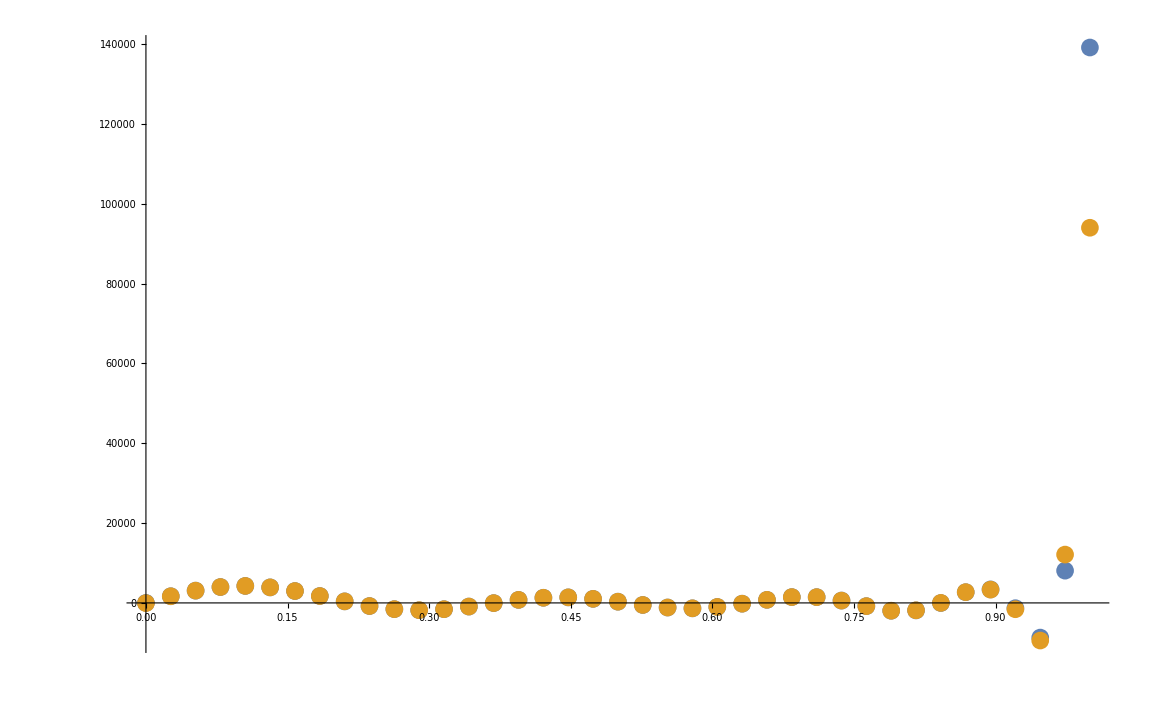

```mathematica
ListPlot[{Transpose[{rg,slaplWnl[9,1,rg]}],Transpose[{rg, fdOp.Wnl[9,1,rg]}]},PlotRange->All]
```